```mathematica
data=Import["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Solid_State_Electronics_Labs\\Band gap\\data.xlsx"];
```

```mathematica
CdSeG1=data[[1]][[42;;87,4;;5]]
```

{{1038.,0.},{1048.7,0.0232558},{1059.4,0.0116279},{1070.1,0.0348837},{1080.8,0.0595238},{1091.5,0.0714286},{1102.2,0.0853659},{1112.9,0.1},{1123.6,0.1125},{1134.3,0.1375},{1145.3,0.153846},{1156.,0.166667},{1166.7,0.197368},{1177.4,0.22973},{1188.1,0.279412},{1198.8,0.333333},{1209.5,0.454545},{1220.2,0.5625},{1230.9,0.645161},{1241.6,0.775862},{1252.3,0.810345},{1263.,0.857143},{1273.7,0.888889},{1284.4,1.09615},{1295.1,1.28846},{1305.8,1.62},{1316.5,2.103},{1327.2,2.68889},{1337.9,3.4633},{1348.6,4.44712},{1359.3,6.23737},{1370.,8.07895},{1380.7,10.3571},{1391.4,12.6989},{1402.1,16.3824},{1412.8,20.5864},{1423.5,25.3871},{1431.07,30.9},{1441.77,36.7931},{1452.37,44.5357},{1463.14,51.3704},{1473.84,55.9023},{1484.54,61.0385},{1495.24,66.6797},{1505.94,72.5},{1516.64,73.08}}

```mathematica
CdSeG2=Transpose[{data[[1]][[42;;87,4]],data[[1]][[42;;87,6]]}]
```

{{1038.,0.},{1048.7,0.000540833},{1059.4,0.000135208},{1070.1,0.00121687},{1080.8,0.00354308},{1091.5,0.00510204},{1102.2,0.00728733},{1112.9,0.01},{1123.6,0.0126563},{1134.3,0.0189063},{1145.3,0.0236686},{1156.,0.0277778},{1166.7,0.0389543},{1177.4,0.0527757},{1188.1,0.0780709},{1198.8,0.111111},{1209.5,0.206612},{1220.2,0.316406},{1230.9,0.416233},{1241.6,0.601962},{1252.3,0.656659},{1263.,0.734694},{1273.7,0.790123},{1284.4,1.20155},{1295.1,1.66013},{1305.8,2.6244},{1316.5,4.42263},{1327.2,7.23012},{1337.9,11.9945},{1348.6,19.7768},{1359.3,38.9048},{1370.,65.2694},{1380.7,107.27},{1391.4,161.261},{1402.1,268.381},{1412.8,423.801},{1423.5,644.505},{1431.07,954.81},{1441.77,1353.73},{1452.37,1983.43},{1463.14,2638.91},{1473.84,3125.06},{1484.54,3725.69},{1495.24,4446.18},{1505.94,5256.25},{1516.64,5340.69}}

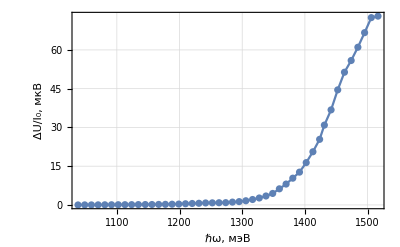

```mathematica
p1=Show[ListPlot[CdSeG1,PlotTheme->"Detailed",FrameLabel->{"ℏω, мэВ","ΔU/I_0, мкВ"}],ListLinePlot[CdSeG1]]
```

```mathematica
ApproximationGaSe=LinearModelFit[CdSeG1[[38;;43]],x,x]["BestFit"]
```

-789.897+0.57392 x

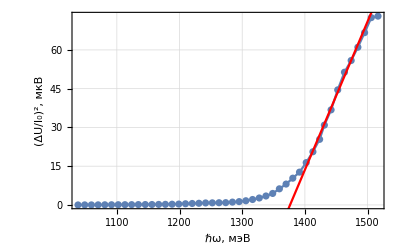

```mathematica
p2=Show[ListPlot[CdSeG1,PlotTheme->"Detailed"],ListLinePlot[CdSeG1],Plot[ApproximationGaSe,{x,1370,1510},PlotStyle->Red],FrameLabel->{"ℏω, мэВ","(ΔU/I_0)^2, мкВ"}]
```

```mathematica
TeXForm[LinearModelFit[CdSeG1[[38;;43]],x,x]["ParameterTable"]]
```

\begin{array}{l|llll}
 \text{} & \text{Estimate} & \text{Standard Error} & \text{t-Statistic} & \text{P-Value} \\
\hline
 1 & -789.897 & 37.1082 & -21.2863 & 0.0000287995 \\
 x & 0.57392 & 0.0254531 & 22.5481 & 0.0000229106 \\
\end{array}

```mathematica
Solve[ApproximationGaSe==0, x]
```

{{x→1376.32}}

```mathematica
Quantity[(x/.Solve[ApproximationGaSe==0,x]),"Millielectronvolts"]+Quantity[50,"Millielectronvolts"]
```

{1426.32 meV}

```mathematica
SiG1=data[[2]][[32;;77,4;;5]]
```

{{985.75,0.},{999.18,0.6742},{1012.61,0.964486},{1026.04,1.52499},{1039.47,2.48807},{1052.9,3.84212},{1066.33,5.96739},{1079.76,8.60233},{1093.19,11.1355},{1106.62,14.3701},{1120.05,17.8023},{1133.48,20.166},{1146.91,23.4876},{1160.34,26.767},{1173.77,29.5727},{1187.2,32.5288},{1200.63,35.4055},{1214.06,37.6143},{1227.49,40.7676},{1240.92,43.494},{1254.35,45.4328},{1267.78,48.4989},{1281.21,50.1332},{1294.64,51.8355},{1308.07,53.6134},{1321.5,54.719},{1334.93,55.1471},{1348.36,55.7215},{1361.79,55.7929},{1375.22,55.4093},{1388.65,55.8949},{1402.08,55.1839},{1415.51,54.9025},{1428.94,54.2825},{1441.37,54.1566},{1455.8,53.7828},{1469.23,53.7977},{1482.66,53.454},{1496.09,53.0842},{1509.52,52.685},{1522.95,52.2529},{1536.38,51.9253},{1549.81,51.0354},{1563.24,50.6674},{1576.67,50.2849},{1590.1,48.8754}}

```mathematica
SiG2=Transpose[{data[[2]][[32;;77,4]],data[[2]][[32;;77,6]]}]
```

{{985.75,0.},{999.18,0.454545},{1012.61,0.930233},{1026.04,2.32558},{1039.47,6.19048},{1052.9,14.7619},{1066.33,35.6098},{1079.76,74.},{1093.19,124.},{1106.62,206.5},{1120.05,316.923},{1133.48,406.667},{1146.91,551.667},{1160.34,716.471},{1173.77,874.545},{1187.2,1058.13},{1200.63,1253.55},{1214.06,1414.84},{1227.49,1662.},{1240.92,1891.72},{1254.35,2064.14},{1267.78,2352.14},{1281.21,2513.33},{1294.64,2686.92},{1308.07,2874.4},{1321.5,2994.17},{1334.93,3041.2},{1348.36,3104.89},{1361.79,3112.84},{1375.22,3070.19},{1388.65,3124.24},{1402.08,3045.26},{1415.51,3014.29},{1428.94,2946.59},{1441.37,2932.94},{1455.8,2892.59},{1469.23,2894.19},{1482.66,2857.33},{1496.09,2817.93},{1509.52,2775.71},{1522.95,2730.37},{1536.38,2696.24},{1549.81,2604.62},{1563.24,2567.19},{1576.67,2528.57},{1590.1,2388.8}}

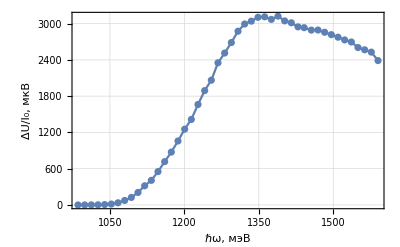

```mathematica
p3=Show[ListPlot[SiG2,PlotTheme->"Detailed",FrameLabel->{"ℏω, мэВ","ΔU/I_0, мкВ"}],ListLinePlot[SiG2]]
```

```mathematica
ApproximationSi=LinearModelFit[SiG1[[8;;24]],x,x]["BestFit"]
```

-214.171+0.207038 x

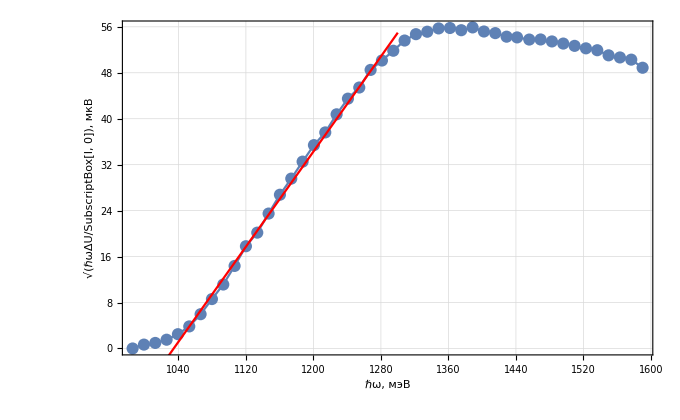

```mathematica
p4=Show[ListPlot[SiG1,PlotTheme->"Detailed"],ListLinePlot[SiG1],Plot[ApproximationSi,{x,1000,1300},PlotStyle->Red],FrameLabel->{"ℏω, мэВ","√(ℏωΔU/SubscriptBox[I, 0]), мкВ"}]
```

```mathematica
TeXForm[LinearModelFit[SiG1[[8;;24]],x,x]["ParameterTable"]]
```

\begin{array}{l|llll}
 \text{} & \text{Estimate} & \text{Standard Error} & \text{t-Statistic} & \text{P-Value} \\
\hline
 1 & -214.171 & 3.83204 & -55.8897 & \text{7.992531724528942$\grave{ }$*${}^{\wedge}$-19} \\
 x & 0.207038 & 0.00322285 & 64.2407 & \text{9.978519627095085$\grave{ }$*${}^{\wedge}$-20} \\
\end{array}

```mathematica
Quantity[(x/.Solve[ApproximationSi==0,x]),"Millielectronvolts"]+Quantity[50,"Millielectronvolts"]
```

{1084.45 meV}

```mathematica
SetDirectory[NotebookDirectory[]]
Export["plot1.pdf",p1];
Export["plot2.pdf",p2];
Export["plot3.pdf",p3];
Export["plot4.pdf",p4];
```

C:\Users\alexn\Documents\GitHub\Labs\Solid_State_Electronics_Labs\Band gap